```mathematica
Taller 10.3
```

```mathematica
Clear[f]
Clear[g]
```

16+ⅇ^(4-x^2)-2 x+3 x Cos[3-x]

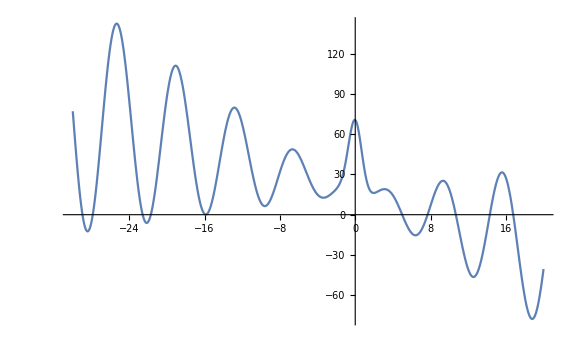

```mathematica
f[x_] := E^(4-x^2)+3*x*Cos[x-3]-2x+16
f[x]
Plot[f[x],{x,-30,20},PlotRange->Automatic,ImageSize->Large]
```

```mathematica
Biseccion
```

```mathematica
Manipulate[Plot[f[x],{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
```

```mathematica
Punto Fijo
```

```mathematica
g[x_] := E^(4-x^2)+3x*Cos[x-3]-x+16
g[x]
Manipulate[Plot[{f[x],g[x],x},{x,negx,posx},PlotRange->{-20,20},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
Manipulate[Plot[{f[x],g'[x],1,-1},{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
```

16+ⅇ^(4-x^2)-x+3 x Cos[3-x]

```mathematica
Newton / Secante
```

```mathematica
f'[x]
g[x_] := x-f[x]/f'[x]
Manipulate[Plot[{f[x],g[x],x},{x,negx,posx},PlotRange->{-20,20},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
Manipulate[Plot[{f[x],g'[x],1,-1},{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
```

-2-2 ⅇ^(4-x^2) x+3 Cos[3-x]+3 x Sin[3-x]

```mathematica
Raices multiples
```

```mathematica
f''[x]
g[x_]:= x-(f[x]*f'[x])/(f'[x]^2-f[x]*f''[x])
Manipulate[Plot[{f[x],g[x],x},{x,negx,posx},PlotRange->{-20,20},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
Manipulate[Plot[{f[x],g'[x],1,-1},{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-30},{posx,20,0}]
```

-2 ⅇ^(4-x^2)+4 ⅇ^(4-x^2) x^2-3 x Cos[3-x]+6 Sin[3-x]